## Differences between primes

```mathematica
results={};n=6;primes=allPrimes[[n]];
```

## Prime 3

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
```

## Visibility Graph

```mathematica
visibles={};Do[
Do[
If[visibleQ[i,j,diffs],AppendTo[visibles,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
g6=Graph[visibles[[;;100]], DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];gv6=Overlay[{g6,Style["d=6", FontFamily->"Times"]}, Alignment->Center, ImageSize->Large];
```

```mathematica
igv6=Graph[visibles, VertexLabels->"Name",VertexLabelStyle->Large,DirectedEdges->False,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv6];
```

```mathematica
count = Total[adj]//Counts
```

```mathematica
count=<|3->106,2->73,4->87,9->15,6->50,15->4,8->28,5->51,13->4,21->3,22->4,37->1,11->12,17->3,10->18,7->17,14->3,12->8,16->2,20->4,31->1,30->1,32->1,23->1,18->1,27->1,19->1|>
```

<|3→106,2→73,4→87,9→15,6→50,15→4,8→28,5→51,13→4,21→3,22→4,37→1,11→12,17→3,10→18,7→17,14→3,12→8,16→2,20→4,31→1,30→1,32→1,23→1,18→1,27→1,19→1|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[;;-2]]
```

{{3,106/9999},{2,73/9999},{4,29/3333},{9,5/3333},{6,50/9999},{15,4/9999},{8,28/9999},{5,17/3333},{13,4/9999},{21,1/3333},{22,4/9999},{37,1/9999},{11,4/3333},{17,1/3333},{10,2/1111},{7,17/9999},{14,1/3333},{12,8/9999},{16,2/9999},{20,4/9999},{31,1/9999},{30,1/9999},{32,1/9999},{23,1/9999},{18,1/9999},{27,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.0222475/x^1.05724]

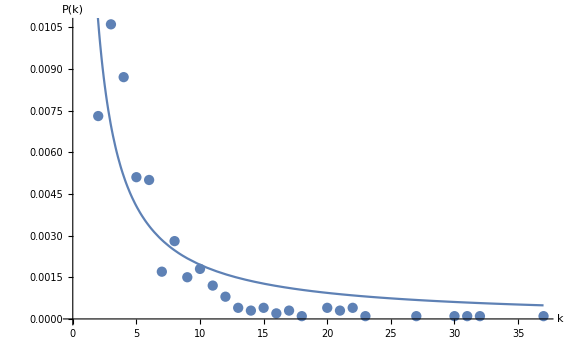

```mathematica
vis6=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-6.eps",vis6];
```

## Mean degree

```mathematica
degree=VertexDegree[igv6]//Mean//N;
```

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n, Length@diffs,degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horizontals={};Do[
Do[
If[horizontalQ[i,j,diffs],AppendTo[horizontals,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
h6=Graph[horizontals[[;;100]], DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];gh6=Overlay[{h6,Style["d=6", FontFamily->"Times"]}, Alignment->Center, ImageSize->Large];
```

```mathematica
igh6=Graph[horizontals, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle->Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh6];
```

```mathematica
count = Total[adj]//Counts
```

<|2→186,4→70,6→35,3→104,8→14,5→48,7→20,9→10,12→3,11→1,13→2,10→6,1→1|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[;;-2]]
```

```mathematica
countrel={{2,93/250},{4,7/50},{6,7/100},{3,26/125},{8,7/250},{5,12/125},{7,1/25},{9,1/50},{12,3/500},{11,1/500},{13,1/250},{10,3/250}}
```

{{2,93/250},{4,7/50},{6,7/100},{3,26/125},{8,7/250},{5,12/125},{7,1/25},{9,1/50},{12,3/500},{11,1/500},{13,1/250},{10,3/250}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x];
```

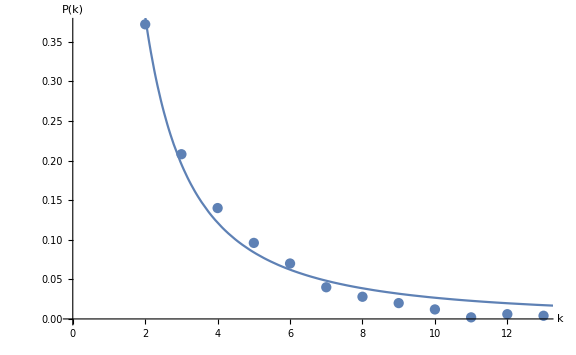

```mathematica
hvis6=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-6.eps",hvis6];
```

## Mean degree

```mathematica
degree=VertexDegree[igh6]//Mean//N;
```

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n, Length@diffs,degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
results
```

{{visibility,6,500,5.876,1.05724 ± 0.296774,0.444905 ± 0.182331},{horizontal,6,500,3.78,0.291843 ± 0.879216,0.0892273 ± 0.133212}}